```mathematica
Clear[func, approxFunc]
func[u_, e_, c_]:=Exp[e(1-c/u)]/(1+Exp[e(1-c/u)])^2
approxFunc[u_, e_, c_]:= 1/4-((c-u)^2 e^2)/(16 u^2)
approxFunc2[u_, e_, c_] := 1/4-((c-u)^2 e^2)/(16 u^2)+((c-u)^4 e^4)/(96 u^4)
```

```mathematica
Solve[1/4-((c-u)^2 e^2)/(16 u^2) == 0, u]
```

{{u→(c e)/(-2+e)},{u→(c e)/(2+e)}}

General::munfl: Exp[-44052.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

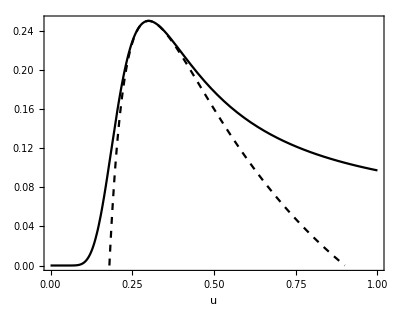

```mathematica
cx=0.3;ex=3;
Show[Plot[{ func[ux, ex, cx] },{ux, 0, 1}, PlotRange->All,PlotStyle->{{Black}}],
Plot[approxFunc[ux, ex, cx],{ux, cx ex/(2 + ex), Min[Abs[cx ex/(-2 + ex)], 1]}, PlotRange->All, PlotStyle->{{Black, Dashed}}],
Frame->True,
FrameLabel->{"u", ""},
FrameStyle->Directive[16],
AspectRatio->0.8
]
```

```mathematica
Integrate[Exp[e(1-c/u)], u]
```

ⅇ^(e-(c e)/u) u+c e ⅇ^e ExpIntegralEi[-(c e)/u]

```mathematica
Series[func[u, e,c], {e, 0, 4}]
```

1/4-((c-u)^2 e^2)/(16 u^2)+((c-u)^4 e^4)/(96 u^4)+O[e]^5

```mathematica
Series[Exp[x]/(1+Exp[x])^2, {x, 0, 4}]
```

1/4-x^2/16+x^4/96+O[x]^5

```mathematica
Integrate[1/4-((c-u)^2 e^2)/(16 u^2), {u, (c e)/(2+e), 1}]
```

$Aborted

```mathematica
Solve[e(1-c/u)==-10, u]
```

{{u→(c e)/(10+e)}}

```mathematica
Integra
```

```mathematica
Integrate[1/4-((c-u)^2 e^2)/(16 u^2),u]
```

(c^2 e^2)/(16 u)+u/4-(e^2 u)/16+1/8 c e^2 Log[u]

```mathematica
(c^2 e^2)/(16 u)+u/4-(e^2 u)/16+1/8 c e^2 Log[u]/.u->1
```

1/4-e^2/16+(c^2 e^2)/16

```mathematica
(c^2 e^2)/(16 u)+u/4-(e^2 u)/16+1/8 c e^2 Log[u]/.u->(c e)/(e-2)
```

(c e)/(4 (-2+e))+1/16 c (-2+e) e-(c e^3)/(16 (-2+e))+1/8 c e^2 Log[(c e)/(-2+e)]

```mathematica
(c^2 e^2)/(16 u)+u/4-(e^2 u)/16+1/8 c e^2 Log[u]/.u-> (c e)/(2+e)
```

(c e)/(4 (2+e))-(c e^3)/(16 (2+e))+1/16 c e (2+e)+1/8 c e^2 Log[(c e)/(2+e)]

```mathematica
1/4-e^2/16+(c^2 e^2)/16 - ((c e)/(4 (2+e))-(c e^3)/(16 (2+e))+1/16 c e (2+e)+1/8 c e^2 Log[(c e)/(2+e)])
```

1/4-e^2/16+(c^2 e^2)/16-(c e)/(4 (2+e))+(c e^3)/(16 (2+e))-1/16 c e (2+e)-1/8 c e^2 Log[(c e)/(2+e)]

```mathematica
Simplify[%]
```

1/16 (4-4 c e-e^2+c^2 e^2-2 c e^2 Log[(c e)/(2+e)])

```mathematica
FullSimplify[%]
```

1/16 (4-4 c e+(-1+c^2) e^2-2 c e^2 Log[(c e)/(2+e)])

```mathematica
(c e)/(4 (-2+e))+1/16 c (-2+e) e-(c e^3)/(16 (-2+e))+1/8 c e^2 Log[(c e)/(-2+e)] - ((c e)/(4 (2+e))-(c e^3)/(16 (2+e))+1/16 c e (2+e)+1/8 c e^2 Log[(c e)/(2+e)])
```

(c e)/(4 (-2+e))+1/16 c (-2+e) e-(c e^3)/(16 (-2+e))-(c e)/(4 (2+e))+(c e^3)/(16 (2+e))-1/16 c e (2+e)+1/8 c e^2 Log[(c e)/(-2+e)]-1/8 c e^2 Log[(c e)/(2+e)]

```mathematica
FullSimplify[(c e)/(4 (-2+e))+1/16 c (-2+e) e-(c e^3)/(16 (-2+e))-(c e)/(4 (2+e))+(c e^3)/(16 (2+e))-1/16 c e (2+e)+1/8 c e^2 Log[(c e)/(-2+e)]-1/8 c e^2 Log[(c e)/(2+e)]]
```

1/8 c e (-4+e Log[(c e)/(-2+e)]-e Log[(c e)/(2+e)])

```mathematica
approxIntegral[e_, c_]:= 1/16 (4-4 c e+(-1+c^2) e^2-2 c e^2 Log[(c e)/(2+e)])
```

```mathematica
approxIntegral2[e_, c_]:=1/8 c e (-4+e Log[(c e)/(-2+e)]-e Log[(c e)/(2+e)])
```

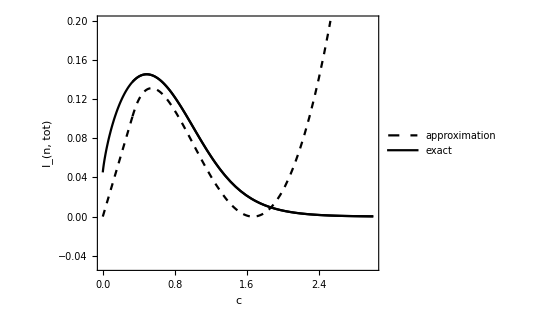

```mathematica
Show[Plot[{approxIntegral[3, cx], NIntegrate[func[ux, 3, cx], {ux, 0,1}]}, {cx, 0.33, 3}, PlotRange->{-0.05, 0.2},  PlotStyle->{{Black, Dashed},{Black}}, PlotLegends->Placed[{"approximation", "exact"}, {0.7, 0.85}]],
Plot[{approxIntegral2[3, cx]}, {cx, 0, 0.333}, PlotRange->{-0.05, 0.2},  PlotStyle->{{Black, Dashed},{Black}}],
Plot[{NIntegrate[func[ux, 3, cx], {ux, 0,1}]}, {cx, 0, 3}, PlotRange->{-0.05, 0.2},  PlotStyle->{{Black}}],

Frame->True,
FrameLabel->{"c", "I_(n, tot)"},
FrameStyle->Directive[16],
AspectRatio->0.8
]
```

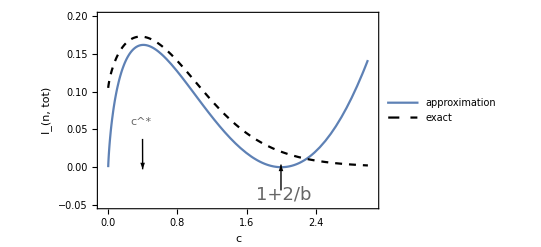

```mathematica
D[approxIntegral2[e, c], c]
```

1/8 e (-4+e Log[(c e)/(-2+e)]-e Log[(c e)/(2+e)])

```mathematica
Solve[1/16 (-4 e-2 e^2+2 c e^2-2 e^2 Log[(c e)/(2+e)])==0, c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c→-ProductLog[-((2+e) ⅇ^(-1-2/e))/e]}}

```mathematica
Solve[1/8 e (-4+e Log[(c e)/(-2+e)]-e Log[(c e)/(2+e)])==0, c]
```

{{}}

```mathematica
Series[-ProductLog[-((2+1/e) ⅇ^(-1-2e))/(1/e)], {e, 0, 2}]
```

(-1)^Floor[(π-2 Arg[e]-Arg[(ⅇ^(-1-2 e) (-1-2 e+ⅇ^(2 e)))/e^2])/(2 π)] O[e]^3+(-1)^Floor[(π-2 Arg[e]-Arg[(ⅇ^(-1-2 e) (-1-2 e+ⅇ^(2 e)))/e^2])/(2 π)] (-2 e+(4 e^2)/3+O[e]^3)+(1+(4 e^2)/3+O[e]^3)

```mathematica
ProductLog[-((2+e) ⅇ^(-1-2/e))/e] /.e->2.0
```

-0.406376

```mathematica
ProductLog[-2.0 Exp[-2]]
```

```mathematica
-0.406Exp[-0.406]
```

-0.270522

```mathematica
-2.0 Exp[-2]
```

-0.270671

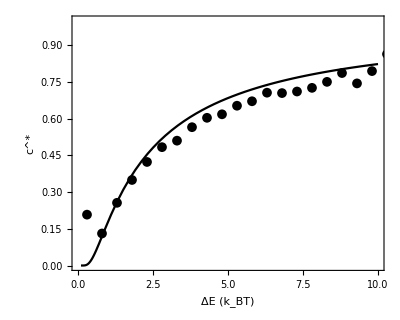

```mathematica
Show[Plot[-ProductLog[-((2+e) ⅇ^(-1-2/e))/e] , {e, 0.1, 10}, PlotRange->{0,1}, PlotStyle->Black],
ListPlot[cTable, PlotMarkers->{Automatic, 10},PlotStyle->Black],
Frame->True,
FrameLabel->{"ΔE (k_BT)", "c^*"},
FrameStyle->Directive[16],
AspectRatio->0.8
]
```

```mathematica
f0=500;
cTable = Table[{ebx,(f0*(xb2-xb1)/kT)/(OptimalN[1, 1.0Exp[-ebx],f0, NagFisherInfo] ebx)}, {ebx,0.3, 15, 0.5}]
```

$Aborted

```mathematica
cTable = {{0.3,0.20791812084600392},{0.8,0.13090979163350286},{1.3,0.2563268647369287},{1.8,0.3496804759682792},{2.3,0.4233224240322512},{2.8,0.48379705603685846},{3.3,0.5103444784401914},{3.8,0.5654542723915369},{4.3,0.6038087288522033},{4.8,0.618185127158208},{5.3,0.6531767381294273},{5.8,0.6714769484649501},{6.3,0.7064972881808091},{6.8,0.704898878026554},{7.3,0.7113363107025956},{7.8,0.7262594500879647},{8.3,0.7507597688861128},{8.8,0.7867810709286284},{9.3,0.7444810133518203},{9.8,0.7948094492034102},{10.3,0.8642588185512811},{10.8,0.824246836210944},{11.3,0.7877757372635571},{11.8,0.880127977648974},{12.3,0.8443504175819425},{12.8,0.8113679793951479},{13.3,0.9370385085345468},{13.8,0.9030878379354691},{14.3,0.8715113401055575},{14.8,0.8420683894263158}};
```

```mathematica
nTable= Table[{ebx,OptimalN[1, 1.0Exp[-ebx],f0, NagFisherInfo] }, {ebx,0.3, 15, 0.5}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
nTable = {{0.3,999},{0.8,595},{1.3,187},{1.8,99},{2.3,64},{2.8,46},{3.3,37},{3.8,29},{4.3,24},{4.8,21},{5.3,18},{5.8,16},{6.3,14},{6.8,13},{7.3,12},{7.8,11},{8.3,10},{8.8,9},{9.3,9},{9.8,8},{10.3,7},{10.8,7},{11.3,7},{11.8,6},{12.3,6},{12.8,6},{13.3,5},{13.8,5},{14.3,5},{14.8,5}};
```

```mathematica
nTable2000= Table[{ebx,OptimalN[1, 1.0Exp[-ebx],2000, NagFisherInfo] }, {ebx,0.3, 15, 0.5}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{0.3,999},{0.8,999},{1.3,759},{1.8,401},{2.3,261},{2.8,189},{3.3,147},{3.8,119},{4.3,99},{4.8,85},{5.3,74},{5.8,66},{6.3,59},{6.8,53},{7.3,49},{7.8,45},{8.3,41},{8.8,37},{9.3,37},{9.8,34},{10.3,32},{10.8,30},{11.3,28},{11.8,27},{12.3,25},{12.8,24},{13.3,23},{13.8,22},{14.3,21},{14.8,20}}

```mathematica
nTable1000= Table[{ebx,OptimalN[1, 1.0Exp[-ebx],1000, NagFisherInfo] }, {ebx,0.3, 15, 0.5}]
```

```mathematica
nTable1000 ={{0.3,999},{0.8,999},{1.3,378},{1.8,199},{2.3,130},{2.8,94},{3.3,73},{3.8,59},{4.3,49},{4.8,42},{5.3,37},{5.8,33},{6.3,29},{6.8,26},{7.3,24},{7.8,22},{8.3,20},{8.8,19},{9.3,18},{9.8,16},{10.3,15},{10.8,15},{11.3,14},{11.8,13},{12.3,12},{12.8,12},{13.3,11},{13.8,11},{14.3,10},{14.8,10}};
```

```mathematica
nTable200= Table[{ebx,OptimalN[1, 1.0Exp[-ebx],200, NagFisherInfo] }, {ebx,0.3, 15, 0.5}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

```mathematica
nTable200 ={{0.3,999},{0.8,229},{1.3,72},{1.8,37},{2.3,25},{2.8,18},{3.3,14},{3.8,11},{4.3,9},{4.8,8},{5.3,7},{5.8,6},{6.3,5},{6.8,5},{7.3,4},{7.8,4},{8.3,4},{8.8,3},{9.3,3},{9.8,3},{10.3,3},{10.8,3},{11.3,2},{11.8,2},{12.3,2},{12.8,2},{13.3,2},{13.8,2},{14.3,2},{14.8,2}};
```

```mathematica
nTable100= Table[{ebx,OptimalN[1, 1.0Exp[-ebx],100, NagFisherInfo] }, {ebx,0.3, 15, 0.5}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

```mathematica
nTable100 = {{0.3,999},{0.8,108},{1.3,34},{1.8,18},{2.3,12},{2.8,8},{3.3,6},{3.8,5},{4.3,4},{4.8,4},{5.3,3},{5.8,3},{6.3,2},{6.8,2},{7.3,2},{7.8,2},{8.3,2},{8.8,2},{9.3,2},{9.8,1},{10.3,1},{10.8,1},{11.3,1},{11.8,1},{12.3,1},{12.8,1},{13.3,1},{13.8,1},{14.3,1},{14.8,1}};
```

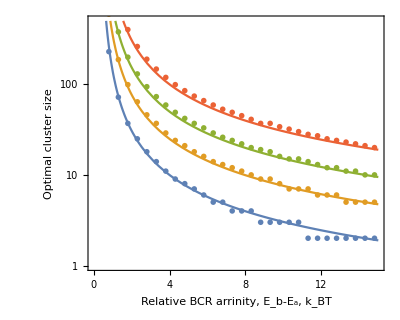

```mathematica
Show[LogPlot[{200*0.5/(-ProductLog[-((2+e) ⅇ^(-1-2/e))/e]e kT) ,500*0.5/(-ProductLog[-((2+e) ⅇ^(-1-2/e))/e]e kT) ,1000*0.5/(-ProductLog[-((2+e) ⅇ^(-1-2/e))/e]e kT) ,2000*0.5/(-ProductLog[-((2+e) ⅇ^(-1-2/e))/e]e kT) }, {e, 0.1, 15}, PlotRange->{{0, 15},{1, 500}}
(*PlotLegends->Placed[{"F=100pN", "F=200pN", "F=500pN", "F=1000pN"}, {0.8, 0.8}]*)
],
ListLogPlot[{nTable200, nTable, nTable1000, nTable2000}, PlotMarkers->{{●, 10}, {●, 10}, {●, 10}, {●, 10}}],
Frame->True,
FrameStyle->Directive[20],
FrameTicksStyle->Directive[16],
AspectRatio->0.8,
FrameLabel->{"Relative BCR arrinity, E_b-E_a, k_BT", "Optimal cluster size"}
]
```

```mathematica
ProductLog
```

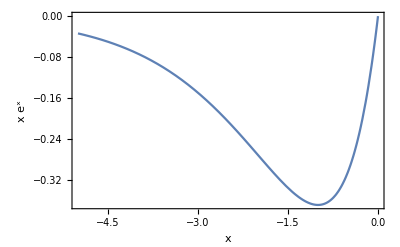

```mathematica
Show[Plot[x Exp[x],{x, -5,0}],
Frame->True,
FrameLabel->{"x", "x e^x"},
FrameStyle->Directive[16]]
```